# Sampling (Distributions)

So what is a distribution in statistics and probability theory ? 
A distribution is a function that shows the possible values for a variable and how often they occur or in other words, 
a distribution is the complete picture of the long run pattern of variability of random variable.

Let’s first clear up a little misconception. A ‘probability function’ as it is, it’s not well defined. 
Generally speaking in statistics and PT when we refer to a ‘probability function’ we generally mean a Probability Mass Function for discrete distributions and a Probability Density Function for continuous distributions. So the term arises when speaking generally about distributions. 

A distribution can be characterized by 5 probability functions :

- the probability density function (pdf), f(t) is defined as the probability of observing an event within a small time interval [t, t + ∆t], as ∆t tends to zero. The pdf is a nonnegative function, f(t) ≥ 0 for all t, provides information about the proportion of the events in any time interval (the frequency of failures in relation to time), and the area between the pdf and the time axes is defined to be unity. Related to space instead of time it gives the probability that x is between two points a and b :

p[a≤x≤b]=∫_a^b f(x)ⅆx
∫_(-∞)^∞ f(x)ⅆx=1
∀x ∈ ℝ ⇒ p(x) ≥ 0

- the cumulative distribution function (cdf ), F(t), is defined as the integral of the pdf over the interval [0, t] and represents the probability that a unit’s lifetime does not exceed time t or the proportion of units whose lifetimes do not exceed time t. It is denoted by F_X(x), where the random variable is the subscript and the realization is the argument. Let look a the properties of the cdf :

0≤F_x(x)≤ 1
x_1 ≥ x_2 ⇒ F_X(x_1) ≥ F_X(x_2)(*ie.monotonically non-decreasing function*)
lim_(n→∞) F_X(x) = 1
lim_(n→-∞) F_X(x) = 0

- the reliability function R(t), often also referred to as the survival function, is defined as the complement of the cdf and corresponds to the probability of a unit to survive up to time t, or the proportion of units that survive up to time t. The reliability function is a nonnegative strictly decreasing function defined as one for t = 0 (the probability of a unit surviving at least to time zero is one) and zero for t = +∞ (the probability of a unit surviving to infinite time is zero).

R(t)=1-F(t)

- the hazard function (hf), is defined as the conditional probability of an item to fail within the time interval [t, t + ∆t], having survived to time t. The hazard function models which periods have the highest or lowest chances of an event. The function is defined as the instantaneous risk that the event of interest happens, within a very narrow time frame. It may be increasing, decreasing, or constant through time and is derived through the following equation:

h(t)=f(t)/R(t)

- the cumulative hazard function (chf ), is defined as the integral of h(t) over the interval [0,t]. The chf is a nonnegative strictly increasing function defined to be zero at t = 0 and + ∞.

H(t) = ∫_0^1 h(u)ⅆu

The pdf is the most common function used to define a distribution, for two reasons :
- the first is that it gives the shape of the density curve, which is the easiest way to recognize and review a distribution.
- the second is that the pdf is always in a useful form, whereas the cdf frequently doesn’t have a closed form.

However take care that every distribution has a cdf (in closed or not closed form) while it’s not always true for the pdf (ie Cantor distribution).

All the five probability functions are mathematically equivalent and if one of them is known, all five can be derived.

- if we have a pdf we can get a cdf, by integration

For example, let’s take the Rayleigh distribution. It’s characterized by the pdf :

```mathematica
(* for piecewise fncs use -> esc pw ese to enter { and ctrl-comma and then ctrl-enter for additional piecewise cases *) 
Clear[pdf,σ,pw];
pw=Piecewise[{{0, x<0}, {x/σ^2 ⅇ^(-x^2/(2 σ^2)), x≥0}}];
pdf[x_]:=x/σ^2 ⅇ^(-x^2/(2 σ^2));
```

Now, let’s integrate the pdf to get the cdf (all are equivalent ways to do that) :

```mathematica
Clear[x];
∫_0^x x/σ^2 ⅇ^(-x^2/(2 σ^2))ⅆx 
∫_0^x pdf[x]ⅆx 
Integrate[pdf[x],{x,0,x}] (* definite integral form *)
```

1-ⅇ^(-x^2/(2 σ^2))

1-ⅇ^(-x^2/(2 σ^2))

1-ⅇ^(-x^2/(2 σ^2))

- if we have a cdf we can get a pdf, by differentiation

```mathematica
Clear[x];
D[1-ⅇ^(-x^2/(2 σ^2)),x] (* D is mathematica simbol for differentiation *)
```

(ⅇ^(-x^2/(2 σ^2)) x)/σ^2

We can use also a custom ProbabilityDistribution build over a cdf and then get its pdf with Mathematica buld-ins

```mathematica
Clear[𝒟,x];
𝒟=ProbabilityDistribution[{"CDF",1-ⅇ^(-x^2/(2 σ^2))},{x,0,∞}]
PDF[𝒟]
```

ProbabilityDistribution[Piecewise[{{(x ⅇ^(-x^2/(2 σ^2)))/σ^2, x>0}, {0, True}}],{x,0,∞}]

Function[x,Piecewise[{{(x ⅇ^(-x^2/(2 σ^2)))/σ^2, x>0}, {0, True}}],Listable]

The derivation of the remaing probability functions is easy and left as an exercise.

========================================================================================
Let’s see some simple practical examples.


Let U be a random variable with a Uniform(0, 1) distribution, and let  X=-Log[1-U]
The goal is to find the pdf of  X.

- First start by identifing the range of possible values of X.
When 
u=0 → -Log[1-u] = -Log[1] = 0
u=1 → -Log[1-u] = -Log[0] = ∞
so X ~ [0,∞]

{Range,0,∞}

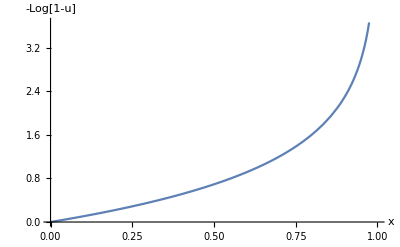

```mathematica
{"Range",Limit[-Log[1-u],u->0],Limit[-Log[1-u],u->1]}
Plot[-Log[1-u],{u,0,1},AxesLabel->{"x","-Log[1-u]"},LabelStyle->Directive[Pink,Bold]]
```

- Then find the cdf, F_X(x)

Now by the definition of the cdf we know that

F_X(x)=P(X≤x)

So just plugin the original eq for X
P(-Log[1-U]≤x)

and solve for U

```mathematica
Clear[U,x];
Solve[-Log[1-U]==x,U]
```

{{U→ConditionalExpression[1-ⅇ^-x,-π≤Im[x]<π]}}

So F_X = 1-e^-x = 1-Exp[-x]

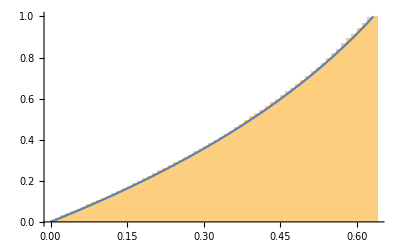

```mathematica
Table[1-Exp[-RandomReal[]],{x,10000}];
Show[
Histogram[%,48, "CDF"],
Plot[-Log[1-u],{u,0,1},PlotRange->{{0,1},{0,1}}]
]
```

Finally, find the pdf by differentiating the cdf with respect to x
f_X(x)=F'(x)=d/dx(1-ⅇ^-x)=

```mathematica
D[1-Exp[-x],x]
```

ⅇ^-x

So our pdf f_X=e^-x

We could have used also this

```mathematica
𝒟=ProbabilityDistribution[{"CDF",1-Exp[-x]},{x,0,∞}];
PDF[𝒟]
```

Function[x,Piecewise[{{ⅇ^-x, x>0}, {0, True}}],Listable]

========================================================================================
Let X be a random variable so that X~𝒰(-1,1) and let Y=X^2, find the distribution of Y.

1

0

1

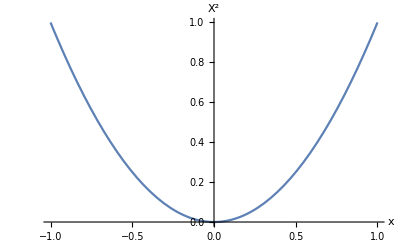

```mathematica
Clear[x,y];
Limit[y=x^2,x->-1]
Limit[y=x^2,x->0]
Limit[y=x^2,x->1]
Plot[x^2,{x,-1,1},AxesLabel->{"x","X^2"},LabelStyle->Directive[Pink,Bold]]
```

So our range of possible values for Y is (0,1)

Now by the definition of the cdf, we know that

F_Y(y)=P(Y≤y)
→P(X^2≤y)

```mathematica
Clear[x,y];
Solve[x^2==y,x]
```

{{x→-√y},{x→√y}}

F_Y(y) = P(-√y≤X≤√y)  (* now, what is the probability that X is between those two values ? *)
= F_X(√y) - F_X(-√y)        (* it’s the  difference of the CDFs evaluated at those two end points *)

Now, we know that the cdf of a uniform distribution in (-1,1) is

```mathematica
UniformDistribution[{-1,1}];
CDF[%]
```

Function[x,Piecewise[{{(1+x)/2, -1≤x≤1}, {1, x>1}, {0, True}}],Listable]

So using that and pluging in our √y, we get

```mathematica
Clear[x,y];
F[x_]=(1+x)/2;
 F[√y] - F[-√y]//Simplify
```

√y

That is the cdf of Y, F_Y=√y
Finally, differentiate to find the pdf

```mathematica
D[√y,y]
```

1/(2 √y)

Let's check it integrates to 1

```mathematica
Integrate[1/(2 √y),{y,0,1}]
```

1

We can also fully use just Mathematica buildins

ProbabilityDistribution[(3 x^2)/2,{x,-1,1}]

Function[x,Piecewise[{{(3 x^2)/2, -1<x<1}, {0, True}}],Listable]

1.

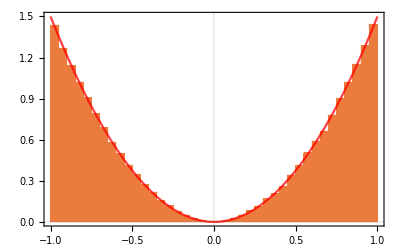

{{x→-√(2/3) √y},{x→√(2/3) √y}}

```mathematica
Clear[𝒟,x,y];
𝒟=ProbabilityDistribution[x^2,{x,-1,1},Method->"Normalize"]
PDF[%]
Integrate[3/2 x^2,{x,-1,1}]//N

Show[
Histogram[RandomVariate[𝒟,10^5],48,PDF,PlotTheme->"Scientific"],
Plot[3/2 x^2, {x,-1,1},PlotStyle->{Red, Opacity[0.75]}]
]
Solve[3/2 x^2==y,x]//FullSimplify
```

```mathematica
Clear[x,y]
Solve[√(2/3) √y==1,y]
```

{{y→3/2}}

========================================================================================

Now, let’s say we wanna ‘sample the distribution’, aka get variates that belongs to a distribution (sometimes it’s referred as simulating a random number with a certain distribution). We can’t use the above Rayleigh distribution because we should have parameterazed it with also the constant σ^2 but we did not for clarity. So we use a buildin gaussian distribution :

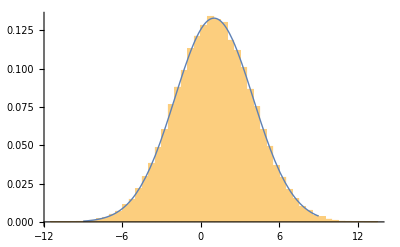

```mathematica
Clear[data];
data=RandomVariate[NormalDistribution[1,3],10^5];
Show[
Histogram[data,64,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,3],x],{x,-9,9},PlotStyle->Thick ]]
```

What we did here? We drawn samples from a normal distribution. Effectively our samples resemble a gaussian distribution (blue line). Another way to put is that we sampled the area under the curve as it is apparent in the graph above.  This may look like a statistical exercise until we use a normal distribution but what if we use a Rayleigh distribution that appears frequently in the equations of rarefied gas dynamics and beam physics ? We’re approaching those dynamics with a stochastic process.


What exactly do we need to be able to sample a certain distribution ? There’re various approaches. Let’s see one.
The method of the inverse cumulative distribution function also called the inversion method (or the method of inverse functions also known as Inversion Sampling, the inverse probability integral transform, the inverse transformation method, Smirnov transform, or the golden rule).

Effectively we saw in part1 that a cdf gives us the probability a random variable X is found at a value equal to or less than a certain x.. ie. how much area is under the curve on the left of a certain point. The inverse cdf gives us the x that bound that area.

We already know how to get the cdf. All we are left to do is to equal the cdf to a random variable and solve for F^-1(x).

ξ=F(x)

y=1-ⅇ^(-x^2/(2 σ^2))

Exp(-x^2/(2 σ^2)) = 1-ξ

-x^2/(2 σ^2) = Log(1-ξ)

x = σ√(-2Log(1-ξ))

Since ξ is uniformly distributed in the interval (0, 1) and because its value has not yet been determined, we can further simplify this expression by noting that ξ and 1 – ξ follow exactly the same probability distribution function. In the sense, it will still be a uniform random number in 0-1. 
However in the realm of floating point numbers it’s better to leave it as 1-ξ because ξ could turn out to be 0 and so we’d take the Log[0] which is undefined while it’s not for Log[1].

Anyway, we arrive at the final expression for the sampling value of x :

x = σ√(-2Logξ)


========================================================================================

Let see another example :

The probability that a neutron has an interaction in dx after having travelled a distance x is given by :

p(x)dx=sⅇ^-sx dx

where s is the total interaction cross section. The pdf is then

p (x) = sⅇ^-sx

and the cdf is

```mathematica
Clear[f,s,x];
fx = s*Exp[-s*x];
∫_0^x fxⅆx
```

1-ⅇ^(-s x)

1-ⅇ^(-s x)

We can now sample the path length x by equating the CDF to a random number ξ, uniformly generated between 0 and 1, and solve for x:

```mathematica
Solve[ξ==1-ⅇ^(-s x),x]
```

{{x→ConditionalExpression[(2 ⅈ π C[1]+Log[1/(1-ξ)])/s,C[1]∈ℤ]}}

Which is 
ξ=1-ⅇ^(-x s_t) → x = (Ln (1 - ξ))/s=(Ln (ξ'))/s

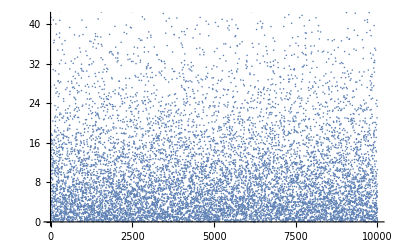

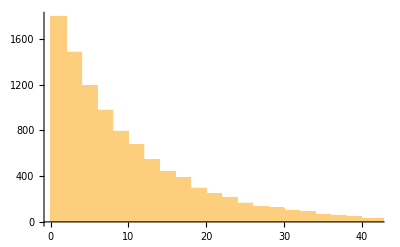

ExponentialDistribution[0.0983247]

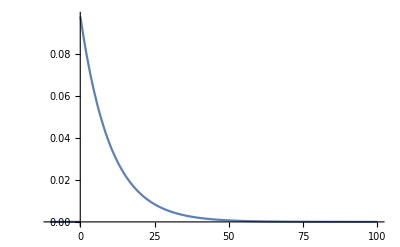

```mathematica
nPathLength[x_,s_:0.1]:=Abs[Log[x]/s];
dddt=Table[nPathLength[RandomReal[{0,1}]],{i,10^4}];
ListPlot[dddt]
Histogram[dddt]

ed=FindDistribution[dddt]
Plot[PDF[ed,x],{x,-10,100},PlotRange->Full]
```

========================================================================================

Another example :
the Cauchy distribution is defined through its density function, get the cdf by integrating the pdf and eventually the inverse cdf :

```mathematica
Clear[fx,x,y];
fx=1/π 1/(1+x^2);
∫_(-∞)^x fxⅆx
Solve[%==y,x]
```

1/2+ArcTan[x]/π

{{x→ConditionalExpression[Tan[1/2 π (-1+2 y)],(-π≤-π+2 π Re[y]<π&&π Im[y]<0)||-π<-π+2 π Re[y]<π||(-π<-π+2 π Re[y]≤π&&π Im[y]>0)]}}

So our cdf is 

1/2+ArcTan[x]/π

and our inverted cdf is

Tan[1/2 π (-1+2 y)]

that simplified will be 

-Cot[π y]

that is our transformation fnc for the Cauchy random variable; where y will be our random number ξ

```mathematica
Simplify[Tan[1/2 π (-1+2 y)]]
```

-Cot[π y]

Btw, if we have to compare two expression to see if they are the same :

```mathematica
FullSimplify[Tan[1/2 π (-1+2 y)]==Tan[π(y-1/2)]]
```

True

```mathematica
Clear[𝒟];
(* check we get back our original pdf from the derived cdf *)
𝒟=ProbabilityDistribution[{"CDF",1/2+ArcTan[x]/π},{x,-∞,∞}];
PDF[𝒟]
```

Function[x,1/((1+x^2) π)]

```mathematica
(* let's do all with mathematica symbols *)
𝒟=ProbabilityDistribution[1/π 1/(1+x^2),{x,-∞,∞}];
CDF[𝒟]
InverseCDF[𝒟,y]
Simplify[%]
```

Function[x,(π+2 ArcTan[x])/(2 π)]

ConditionalExpression[Piecewise[{{-∞, y≤0}, {∞, y≥1}, {Tan[1/2 (-π+2 π y)], True}}],0≤y≤1]

ConditionalExpression[Piecewise[{{-∞, y≤0}, {∞, y≥1}, {-Cot[π y], True}}],0≤y≤1]

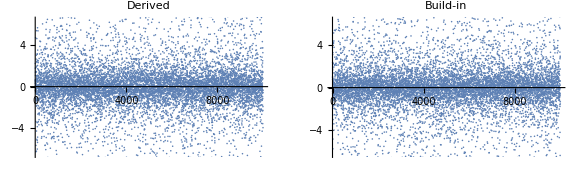

```mathematica
(* visually compare ours vs buildin random variate outcome *)
cauchyOur=Table[-Cot[RandomReal[{0,1}]*π],{i,10^4}];
cauchyBuildin = Table[RandomVariate[CauchyDistribution[0,1]], {i,10^4}];

GraphicsRow[{ListPlot[cauchyOur,PlotLabel->"Derived"],ListPlot[cauchyBuildin,PlotLabel->"Build-in"]},PlotLabel->Style[Framed["Compare",RoundingRadius->5,FrameStyle->Directive[Brown,Dotted]],12,RGBColor[0.5,0.68,0.91]]]
```

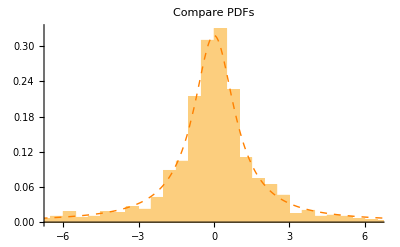

```mathematica
Clear[data];
SeedRandom[12345];
data=Table[-Cot[RandomReal[{0,1}]*π],{i,10^3}];
Show[
Histogram[data,Automatic,"ProbabilityDensity"],
Plot[PDF[CauchyDistribution[0,1],x],{x,-8,8},PlotStyle->{Orange,Dashed,Thick}],
PlotLabel->"Compare PDFs"]
```

========================================================================================

A different case could be when we have a probability function (pf) and we don't know what is it .. a pdf ? 
So first let's try to integrate it over its domain to see if goes to 1 (aka it's a pdf) :

```mathematica
Clear[pf];
pf=Sin[x] Exp[-x];
Integrate[pf,{x,0,Pi}]
```

1/2 (1+ⅇ^-π)

So the pf is not a pdf. Let’s use Mathematica to normalized it :

```mathematica
uv𝒟=ProbabilityDistribution[pf,{x,0,Pi},Method->"Normalize"]
```

ProbabilityDistribution[(2 ⅇ^-x Sin[x])/(1+ⅇ^-π),{x,0,π}]

```mathematica
Integrate[(2 ⅇ^-x Sin[x])/(1+ⅇ^-π),{x,0,Pi}]
```

1

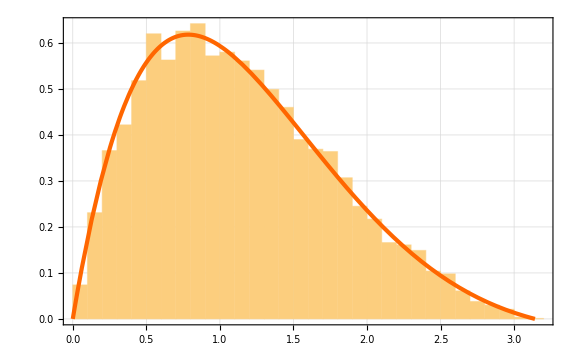

```mathematica
Show[
Histogram[RandomVariate[uv𝒟,10^4],Automatic,PDF,PlotTheme->"Detailed"],  (* sample the distribution *)
Plot[PDF[uv𝒟,x],{x,0,Pi},PlotTheme->"Marketing"],ImageSize->Large               (* effective density function to compare against *)
]
```

This is even more apparent. Let’s say we have the following Integral

1/3

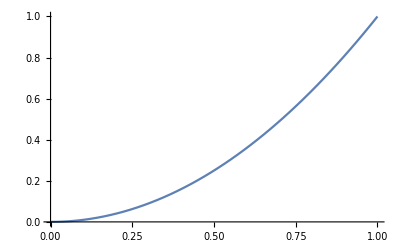

```mathematica
Clear[x,i];
i=∫_0^1 x^2 ⅆx
Plot[x^2,{x,0,1},PlotRange->Full]
```

Now, it’s easy to see that to make x^2 an actual PDF we need to add a normalizing coeff of 3, 
so that 3 x^2 will integrate to 1 (as before was integrating to 1/3)... 1/3 *3 = 1. 
Let’s see it with Mathematica :

ProbabilityDistribution[3 x^2,{x,0,1}]

1.

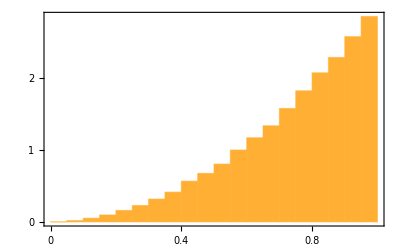

```mathematica
Clear[𝒟,x];
𝒟=ProbabilityDistribution[x^2,{x,0,1},Method->"Normalize"]
Integrate[3 x^2,{x,0,1}]//N
Histogram[RandomVariate[𝒟,10^5],Automatic,PDF,PlotTheme->"Web"]
```

========================================================================================

Normalizing constant and the Box-Muller method

The normalizing constant is used to reduce any probability function to a probability density function with total probability of one. In probability theory, a normalizing constant is a constant by which an everywhere non-negative function must be multiplied so the area under its graph is 1, e.g., to make it a probability density function.

Let’s start with a Gaussian function

p(x)=ⅇ^(-x^2/2), x ϵ (-∞,∞)

we have the corresponding Gaussian integral

∫_(-∞)^∞ p(x)ⅆx = ∫_(-∞)^∞ ⅇ^(-x^2/2)ⅆx = √(2π)

If we use the latter’s reciprocal value as a normalizing constant for the former, defining a function φ(x) as

φ(x)=1/(√(2π))p(x)=1/(√(2π))ⅇ^(-x^2/2)

so the integral is unit

∫_(-∞)^∞ φ(x)ⅆx=∫_(-∞)^∞ 1/(√(2π))ⅇ^(-x^2/2)ⅆx=1

```mathematica
Clear[x];
∫_(-∞)^∞ 1/(√(2π))ⅇ^(-x^2/2)ⅆx
```

1

then the function φ(x) is a probability density function and the constant 1/(√(2π))is the normalizing constant of the Gaussian function p(x).

We can find a pdf from a function as the latter example above, with  Mathematica functions :

```mathematica
Clear[n,x,uv𝒟];
uv𝒟=ProbabilityDistribution[ⅇ^(-x^2/2),{x,-∞,∞},Method->"Normalize"];
PDF[uv𝒟]

(* and eventually extract the constant with *)
Solve[n*Exp[-x^2/2]==1/(√(2π))Exp[-x^2/2],n]
```

Function[x,(ⅇ^(-x^2/2))/(√(2 π))]

{{n→1/(√(2 π))}}

Or directly find the normalizing constant in this way :

```mathematica
Clear[x,n];
Ψ[x_]:=n Exp[-x^2/2];
condition=Integrate[Ψ[x],{x,-∞,∞}]==1;
Solve[condition,n]
```

{{n→1/(√(2 π))}}

========================================================================================

So we introduced the normalizing constant to a Gaussian function to get the Gaussian integral. Now let’s see the
Box-Muller method for sampling a normal gaussian distribution using stochastic variables with a uniform distribution (effectively (there is no closed-form expression for the distribution function of a standard normal so we can’t use the inversion method).

We start where we started for the normalizing constant

∫_(-∞)^∞ p(x)ⅆx = ∫_(-∞)^∞ ⅇ^(-x^2/2)ⅆx = √(2π)

this time in order to prove the above, we introduce

(∫_(-∞)^∞ ⅇ^(-x^2/2)ⅆx)^2=∫_(-∞)^∞ ⅇ^(x^2+y^2/2)ⅆxⅆy

and replace x and y with r and θ .. (if x and y are two points in the Cartesian plane they can be represented in polar coordinates with a radius r and an angle \theta)
-Graphics-

x=r Cosθ
y =r Sinθ

this develop as

x^2+y^2=r^2
Tan^-1 y/x=θ

Notice that if r ≤ 1 and theta ϵ [0 , 2pi], then we map out values contained in the unit circle, as shown in the figure below. Also note that random variables in such a circle can be generated by transforming values sampled from the uniform distribution. Specifically, radii can be sampled from r ~ U(0,1) and angle can be sampled from theta ~ 2pi * U(0,1). A similar mechanism (i.e. drawing points in a circle using uniform variables) is at the heart of the Box-Muller transform for sampling Normal random variables (https://theclevermachine.wordpress.com/2012/09/11/sampling-from-the-normal-distribution-using-the-box-muller-transform/)

(∂(x,y))/(∂(r,θ)=r

Being the latter a Jacobian, we show that

∫_(-∞)^∞ ⅆxⅆy ⅇ^(x^2+y^2/2)=∫_0^(2π) ⅆθ∫_0^∞ ⅆ rrⅇ^(-r^2/2)=2π∫_0^∞ ⅇ^-u ⅆu (where u=r^2/2)=2π((-ⅇ^-u)_0)^∞=2π

therefore eq.1 is true, same for the following

1=1/(2π)∫_(-∞)^∞ ⅇ^(-(x^2+y^2/2))

Now let’s define a new function like

U(R)=1/(2π)∫_(x^2+y^2≤R^2) ⅇ^(-(x^2+y^2/2))

the integral interval is in x^2+y^2≤R^2

U(R)=1/(2π)∫_0^(2π) ⅆθ∫_0^R ⅆ rrⅇ^(-r^2/2)=∫_0^(R^2/2) ⅇ^-u ⅆu=1-ⅇ^(-R^2/2)

Now as of all the above

U(R)=p⇒R=√(-2Log[1-p])

where s=1-p ϵ (0,1) and t ϵ (0,1)

x=Piecewise[{{√(-2Log[s]), Cos[2πt]}, {√(-2Log[s]), Sin[2πt]}}]

Eventually, generalized
z=μ+σ √(-2Log[s])Cos[2πt]
z=μ+σ √(-2Log[s])Sin[2πt]

So basically the procedure for the Box-Muller method is to draw two uniform indipendent variates, 
one for R and another for θ and then transform’em into Cartesian coordinates.

{0.518894,-0.347695}

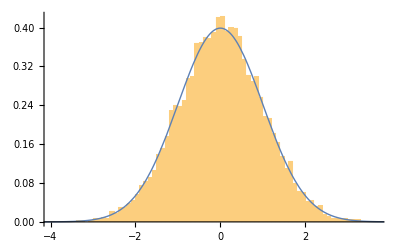

```mathematica
boxMuller[s_,t_]:=Module[{},
r=√(-2Log[s]);
{r*Cos[2π*t],r*Sin[2π*t]}];(* with two uniform variates get two normal variates *)
boxMuller[RandomReal[],RandomReal[]]

SeedRandom[123456];
ggx:=√(-2Log[RandomReal[]])Cos[2π*RandomReal[]]
data=Table[ggx,{i,10^4}];

Show[
Histogram[data,64,"PDF"],
Plot[PDF[NormalDistribution[],x],{x,-9,9},PlotStyle->Thick,PlotRange->Full ]]
```

========================================================================================

There are other methods for drawing random variates from distributions as the inversion method can't be always used because while a cdf is always available what is not it's his inverse. Another populare method is the rejection sampling.

How works Rejection Sampling

Assume that we want to draw samples from a target distribution, p(x) that is hard or impossible to directly sample from. But we have a method to draw samples from another distribution that is easy to sample from, called the proposal distribution, q(x).  Given a sample from the proposal distribution, we can calculate its probability from the target distribution and then keep the sample if it is a true draw, but reject it if not. How do we know if it is representative of a true draw from the target distribution?

We want to draw samples from this target distribution p𝒟:

```mathematica
Clear[p𝒟,q𝒟];
p𝒟=MixtureDistribution[{2,1},{CauchyDistribution[],NormalDistribution[1,1/5]}];
PDF[p𝒟]
Plot[PDF[p𝒟,x],{x,-3,4},Filling->Axis,PlotRange->Full]
```

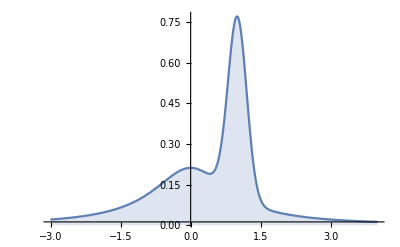

```mathematica
Function[x,]
```

but the only algorithm we have to draw samples from, is this one:

```mathematica
q𝒟 = NormalDistribution[.5,1];
```

The idea is to first find M such that p(x) < M × q(x), i.e. that PDF[p𝒟,x] < M* PDF[q𝒟,x]. 
Ie. we want M × q(x) to be higher than p(x) over the range where p(x)>0.

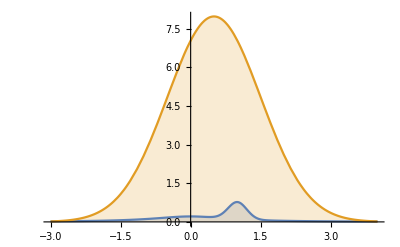

```mathematica
Plot[{PDF[p𝒟,x],20*PDF[q𝒟,x]},{x,-3,4},Filling->Axis]
```

Now draw a sample x’ from the proposal distribution, q𝒟, and another sample, u,  from the uniform distribution (between 0 and 1). 
Only count the sample x’, if u*M*PDF[q𝒟,x’] < PDF[p𝒟,x’].

Effectively, we are drawing a sample from a uniform distribution between 0 and M × q(x), and testing if it’s probability is below p(x).

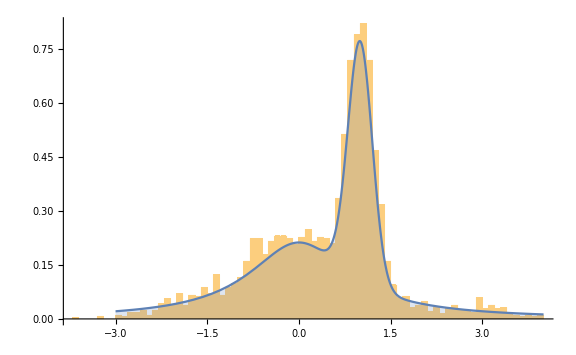

```mathematica
Clear[x,u,M,gH,gp𝒟];
SeedRandom[1234];
x:=RandomVariate[q𝒟 ];
u := RandomVariate[UniformDistribution[]];
M = 3;

samples=Table[If[(u<(PDF[p𝒟,x0=x]/(M*PDF[q𝒟,x0])) && Abs[x]<3),
x0,(*else*)
Null],
{10^4}];

gH=Histogram[samples,64,"PDF"];
gp𝒟=Plot[{PDF[p𝒟,x]},{x,-3,4},Filling->Axis,PlotRange->Full];
Show[{gH,gp𝒟},ImageSize->Large]
```

Rejection sampling becomes increasingly inefficient as the dimensionality increases when too many samples get rejected. It has also problems where there’re narrow peaks in the distribution as there there will be many sample discarded.

========================================================================================

Importance Sampling

we don’t use it to directly produce samples from a distribution, but use samples from a proposal distribution to estimate expectations with respect to the target distribution. If we sample x from p(x):

E[f] = ∫f(x)p(x)ⅆx ~ (1/N∑)_i^N f(x^i)

But if we sample x from q(x), then the expectation of f(x)p(x)/q(x) (with respect to sampling from q) is :

E[f] = ∫(f(x) (p(x))/(q(x)))q(x)ⅆx = ∫(f(x) w(x))q(x)ⅆx  ~ (1/N∑)_i^N f(x^i)w(x^i)

Lets look at an example where we find the average of a random variable from target distribution p𝒟, but we don’t sample from it directly--as before, we sample from a proposal distribution, q𝒟. In this case, let f(x) = x.

```mathematica
Clear[q𝒟,p𝒟,u,weights,x,xsamples];
q𝒟 = NormalDistribution[0,3];
p𝒟 = NormalDistribution[3,1];

u := RandomVariate[q𝒟];
weights=Table[{x0=u,PDF[p𝒟,x0]/PDF[q𝒟,x0]},{1000}];
Mean[weights[[;;,1]]*weights[[;;,2]]]

(* Compare with the mean when we are allowed to directly sample from p𝒟: *)
x:=RandomVariate[p𝒟 ]; 
xsamples=Table[{x},{1000}];
Mean[xsamples]
```

3.06046

{2.98501}

Now, suppose we need to sample from a truncated normal distribution with support from 0 to 1--call it p_T(x). 
We could draw samples from the normal and throw out ones outside of the (0,1) range. 
This could waste many samples. 

Alternatively, we could use the uniform distribution over (0,1) as the proposal distribution, 
and weight each sample by the truncated normal, p_T(x^i) / 𝒰[0,1] = p_T(x^i) /1. 
You can show that the mean is:

(1/N) ∑_i^N x^i p_T(x^i)

And so, - every sample gets used.

```mathematica
𝒟trunc=TruncatedDistribution[{0,1},NormalDistribution[]];
u := RandomVariate[UniformDistribution[{0,1}]];

(* Mathematica provides an analytic formula for the mean *)
Mean[𝒟trunc]
N[%]

(* But we can also estimate the mean using importance sampling *)
Table[{x0=u ,x0*PDF[𝒟trunc,x0]},{10000}];
Mean[%]
```

((-1+√ⅇ) √(2/(ⅇ π)))/Erf[1/(√2)]

0.459862

{0.502183,0.461406}

========================================================================================
[https://blog.demofox.org/2018/06/12/monte-carlo-integration-explanation-in-1d/]

Here the importance sampling function is Sin[x] and the function to sample is Sin[x]^2. 
We can see that the former encloses the latter so we can use it to generate samples from there. We just need to account for the importance function being used instead of a uniform one by dividing by the pdf of that function.

Sin[x]/2

Sin[x/2]^2

{{x→ConditionalExpression[2 (-ArcSin[√y]+2 π C[1]),C[1]∈ℤ]},{x→ConditionalExpression[2 (π-ArcSin[√y]+2 π C[1]),C[1]∈ℤ]},{x→ConditionalExpression[2 (ArcSin[√y]+2 π C[1]),C[1]∈ℤ]},{x→ConditionalExpression[2 (π+ArcSin[√y]+2 π C[1]),C[1]∈ℤ]}}

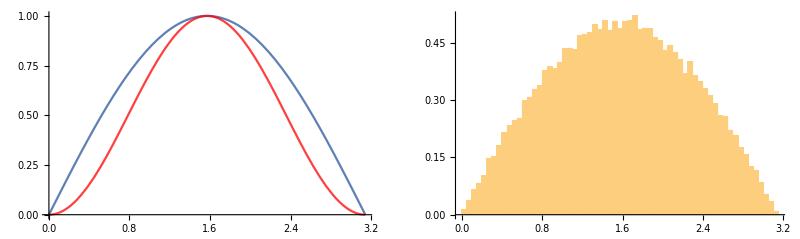

{True,1.5708,Estimate,1.57137}

```mathematica
Clear[x,y];
(* automatically normalize to get a PDF *)
PDFis=Sin[x]/Integrate[Sin[x],{x,0,π}] 
CDFis=Integrate[PDFis,{x,0,x}]
inverseCDF=Solve[CDFis==y,x]
(* check sampler works correctly*)
Table[2*ArcSin[√RandomReal[]],{i,10^5}];
GraphicsRow[{Show[Plot[Sin[x],{x,0,π}],Plot[Sin[x]^2,{x,0,π},PlotStyle->{Red, Opacity[0.75]}]],
Histogram[%,64,"PDF"]},ImageSize->Full]
pdf[k_]:=Sin[k]/2;
icdf[w_]:=2*ArcSin[Sqrt[w]];
sample:=Block[{},
s=RandomReal[];
j=icdf[s];
y=Sin[j]*Sin[j];
y/pdf[j]]
(* simulate *)
nsamples=10^5;
trueval=N[ ∫_0^π Sin[x]^2ⅆx,6 ];
estimates=Table[sample,{i,nsamples}];
estimated = Total[estimates]/nsamples;
{"True",trueval,"Estimate",estimated}
```

```mathematica
Sqrt[Total[(estimates-trueval)^2]/Length[estimates]]
Sqrt[Total[(estimates-estimated)^2]/(Length[estimates]-1)]
StandardDeviation[estimates]
```

0.44663

0.446631

0.446631

See ‘Monte Carlo Simulations in Physics’ pg16 for more on ImportanceSampling
MultipleImportanceSampling : https://64.github.io/multiple-importance-sampling

TODO: 

-> https://bookdown.org/kevin_davisross/probbook/sec-cdf-method.html
-> https://bookdown.org/kevin_davisross/probbook/law-of-the-unconscious-statistician.html

-> https://www.scratchapixel.com/lessons/mathematics-physics-for-computer-graphics/monte-carlo-methods-mathematical-foundations/sampling-distribution
-> https://www.scratchapixel.com/lessons/mathematics-physics-for-computer-graphics/monte-carlo-methods-in-practice/monte-carlo-integration